```mathematica
SetDirectory["/Users/adrianbaule/Library/Mobile Documents/com~apple~CloudDocs/Projects/2025/shearjamming/Data"];
```

```mathematica
data1=Import["phi0p752.dat"];(*Dataset for phi=0.752, not DST*)
data2=Import["phi0p758.dat"];(*Dataset for phi=0.758*)
data3=Import["phi0p764.dat"];(*Dataset for phi=0.764, DST*)
```

```mathematica
nnodes=2000; (*nodes=number of particles*)
fdim=5; (*feature dimension*)
newfdim=10; (*new feature dimension or embedding dimension*)
mconst=-10;
diagmask=ConstantArray[1,{nnodes,nnodes}]-IdentityMatrix[nnodes]; (*Mask removes self-attention weights*) 
particlegatsig=NetGraph[<|"xvals"->PartLayer[{All,1}],"yvals"->PartLayer[{All,2}],"xleft"->ReshapeLayer[{1,All}],"xright"->ReshapeLayer[{All,1}],"yleft"->ReshapeLayer[{1,All}],"yright"->ReshapeLayer[{All,1}],"xneg"->ElementwiseLayer[-#&],"yneg"->ElementwiseLayer[-#&],"xrelmatrix"->ThreadingLayer[Plus],"yrelmatrix"->ThreadingLayer[Plus],"rleft"->ReshapeLayer[{1,All}],"rright"->ReshapeLayer[{All,1}],"rsum"->ThreadingLayer[Plus],"contact"->ThreadingLayer[If[√(#1 #1+#2 #2)<#3,1,0]&],"nodiagarray"->NetArrayLayer["Array"->diagmask],"nodiag"->ThreadingLayer[#1*#2&],"W"->NetArrayLayer["Output"->{fdim,newfdim}],"wdot"->DotLayer[],"asrc"->NetArrayLayer["Output"->newfdim],
"atarg"->NetArrayLayer["Output"->newfdim],"dotsrc"->DotLayer[],"dottarg"->DotLayer[],"left"->ReshapeLayer[{1,All}],"right"->ReshapeLayer[{All,1}],"outersum"->ThreadingLayer[Plus],"leaky"->ElementwiseLayer[If[#>0,#,0.2#]&],"masking"->ThreadingLayer[#1 #2+(1-#1)mconst&],"siggat"->ElementwiseLayer[1/(1+Exp[-#])&],"adoth"->DotLayer[],"nlin"->ElementwiseLayer[1/(1+Exp[-#])&],"W2"->LinearLayer[nnodes,Input->{nnodes,newfdim}],"nlin2"->ElementwiseLayer[1/(1+Exp[-#])&],"W3"->LinearLayer[nnodes,Input->nnodes],"softmax2"->SoftmaxLayer[],"dotprob"->DotLayer[]|>,{NetPort["positions"]->"xvals"->"xleft","xvals"->"xneg"->"xright",NetPort["positions"]->"yvals"->"yleft","yvals"->"yneg"->"yright",{"xleft","xright"}->"xrelmatrix",{"yleft","yright"}->"yrelmatrix",NetPort["radii"]->"rleft",NetPort["radii"]->"rright",{"rleft","rright"}->"rsum",{"xrelmatrix","yrelmatrix","rsum"}->"contact",{"nodiagarray","contact"}->"nodiag",{NetPort["features"],"W"}->"wdot",{"wdot","asrc"}->"dotsrc"->"left",{"wdot","atarg"}->"dottarg"->"right",{"left","right"}->"outersum"->"leaky",{"nodiag","leaky"}->"masking"->"siggat",{"siggat","wdot"}->"adoth"->"nlin"->"W2"->"nlin2"->"W3"->"softmax2",{"nlin2","softmax2"}->"dotprob"}]
```

NetGraph[<35>, <45>]

```mathematica
packings1={};
packings3={};
Do[AppendTo[packings1,data1[[1+2000(10i);;2000(10i+1)]]],{i,0,99}] (*select every 10th packing*)
Do[AppendTo[packings3,data3[[1+2000(10i);;2000(10i+1)]]],{i,0,99}]
```

```mathematica
nodeset={}; (*node features in columns (2,5,7,9,11)*)
posset={}; (*particle positions in columns (3,4)*)
radset={}; (*particle radii to determine contact network in column 2*)
labels={}; (*DST or not*)
Do[{packing=packings1[[i]];
AppendTo[nodeset,packing[[All,{2,5,7,9,11}]]];
AppendTo[posset,packing[[All,{3,4}]]];
AppendTo[radset,packing[[All,2]]];
AppendTo[labels,False]},{i,1,Length[packings1]}] (*Data 1 is not DST*)
Do[{packing=packings3[[i]];
AppendTo[nodeset,packing[[All,{2,5,7,9,11}]]];
AppendTo[posset,packing[[All,{3,4}]]];
AppendTo[radset,packing[[All,2]]];
AppendTo[labels,True]},{i,1,Length[packings3]}](*Data 3 is DST*)
```

```mathematica
trainedgat=NetTrain[particlegatsig,<|"features"->nodeset,"positions"->posset,"radii"->radset,"Output"->labels|>,LearningRate->0.0001,ValidationSet->Scaled[0.2]]
```

NetGraph[<35>, <45>]

```mathematica
subnet=NetTake[trainedgat,{All,"siggat"}](*Extract the alpha weights from the "siggat" layer*)
```

NetGraph[<28>, <36>]

```mathematica
index=1030; (*Testing a specific packing*)
packingtest=data1[[1+nnodes index;;nnodes (index+1)]];
nodetest=packingtest[[All,{2,5,7,9,11}]];
postest=packingtest[[All,{3,4}]];
radtest=packingtest[[All,2]];
trainedgat[<|"features"->nodetest,"positions"->postest,"radii"->radtest|>](*Output DST or not*)
alphamatrix=subnet[<|"features"->nodetest,"positions"->postest,"radii"->radtest|>];(*Output the alpha weights*)
```

False

```mathematica
alphas={};
Do[Do[{alphaval=alphamatrix[[i,j]];
If[alphaval>0.0001,Block[{},AppendTo[alphas,alphaval]]]},{j,1,nnodes}],{i,1,nnodes}](*Convert alpha matrix values to list of non-zero alpha weights*)
```

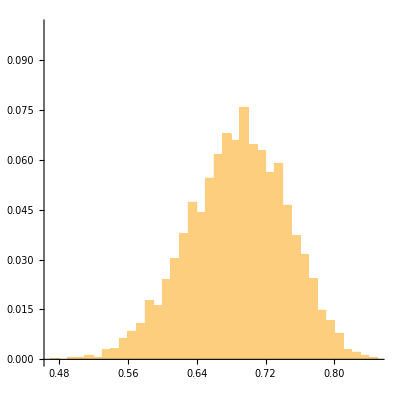

```mathematica
Histogram[alphas,40,"Probability",PlotRange->{Automatic,{0,0.1}},AspectRatio->1]
```